```mathematica
SetDirectory["C:/Users/Jacqui/Documents/CU_Boulder/MathBio/Aging/ReactionDiffusionModel2016"]
```

C:\Users\Jacqui\Documents\CU_Boulder\MathBio\Aging\ReactionDiffusionModel2016

```mathematica
(* REvaluate["install.packages('nleqslv')"] *)
```

```mathematica
Needs["RLink`"]
```

```mathematica
InstallR[]
```

```mathematica
(* Import R Function patternSpace to use to create Countour Plots*)
patternSpace= REvaluate[Import["Scripts/patternSpace.R"]]
```

RFunction[closure,RCode[function (km, ki, h, r, d, gamma) 
{
    library(nleqslv)
    setwd("C:/Users/Jacqui/Documents/CU_Boulder/MathBio/Aging/ReactionDiffusionModel2016/")
    source("Scripts/RDSystemFunctions.R")
    assign("km", km, envir = .GlobalEnv)
    assign("ki", ki, envir = .GlobalEnv)
    assign("h", h, envir = .GlobalEnv)
    assign("r", r, envir = .GlobalEnv)
    assign("a", 1, envir = .GlobalEnv)
    assign("b", 1, envir = .GlobalEnv)
    assign("c", 1, envir = .GlobalEnv)
    l1 = 1
    l2 = 0.2
    ss = nleqslv(c(1, 1), dslnex)
    u0 = ss$x[1]
    v0 = ss$x[2]
    derivs = findDerivatives(a, b, c, h, km, ki, r, u0, v0)
    fu = derivs[1]
    fv = derivs[2]
    gu = derivs[3]
    gv = derivs[4]
    mode_df = findModes(fu, fv, gu, gv, gamma, d, l1, l2)
    return(nrow(mode_df))
}],1,RAttributes[]]

```mathematica
patternSpaceWrapper[km_,ki_,h_,r_] := (
RSet["x",km];
RSet["y",ki];
RSet["z",h];
RSet["zz",r];
REvaluate["N = patternSpace(x,y,z,zz,5,80);"];
Return[REvaluate["N"]]
)
```

```mathematica
(* Make a 2D Countour Plot *)
ContourPlot[patternSpaceWrapper[kdb,kda, 0.0001, 10],{kdb,0,.09},{kda,0,.09},FrameLabel -> {"kdb","kda"},Contours->{0.5,1.5,2.5,3.5,4.5,5.5},MaxRecursion->5]
```

RSet::badval: The expression kdb is not convertable to R

RSet::badval: The expression kda is not convertable to R

-Graphics-

```mathematica
ContourPlot[patternSpaceWrapper[kdb,kda, 0.0001,5],{kdb,0,.09},{kda,0,.09},FrameLabel -> {"kdb","kda"},Contours->{0.5,1.5,2.5,3.5,4.5,5.5},MaxRecursion->5]
```

RSet::badval: The expression x is not convertable to R

RSet::badval: The expression y is not convertable to R

-Graphics-

```mathematica
ContourPlot[patternSpaceWrapper[kdb,kda, 0.0001, 10],{kdb,0.001,200},{kda,0.001,200},FrameLabel -> {"kdb","kda"},Contours->{0.5,1.5,2.5,3.5,4.5,5.5},MaxRecursion->10]
```

RSet::badval: The expression x is not convertable to R

RSet::badval: The expression y is not convertable to R

-Graphics-

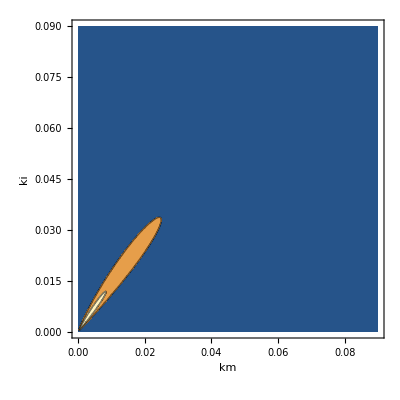

```mathematica
ContourPlot[patternSpaceWrapper[kdb,kda, 0.001, 10],{kdb,0,.09},{kda,0,.09},FrameLabel -> {"kdb","kda"},Contours->{0.5,1.5,2.5,3.5,4.5,5.5},MaxRecursion->5]
```

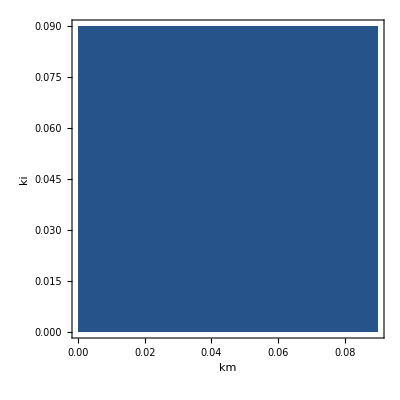

```mathematica
ContourPlot[patternSpaceWrapper[kdb,kda, 0.01, 10],{kdb,0,.09},{kda,0,.09},FrameLabel -> {"kdb","kda"},Contours->{0.5,1.5,2.5,3.5,4.5,5.5},MaxRecursion->5]
```

```mathematica
(* Generate a 3D Countour plot of kda kdb and h *)
ContourPlot3D[patternSpaceWrapper[kdb,kda, h, 10],{kdb,0,.09},{kda,0,.09},{h,0.0001,.001},Contours->{0.5,1.5,2.5,3.5,4.5,5.5},ContourStyle->Opacity[0.4],MaxRecursion->1]
```

-Graphics3D-

```mathematica
(* Import R Function reactionConstraints to use to create Countour Plots*)
patternSpace= REvaluate[Import["Scripts/reactionConstraints.R"]]
```

RFunction[closure,RCode[function (km, ki, h, r) 
{
    library(nleqslv)
    setwd("C:/Users/Jacqui/Documents/CU_Boulder/MathBio/Aging/ReactionDiffusionModel2016/")
    source("Scripts/RDSystemFunctions.R")
    assign("km", km, envir = .GlobalEnv)
    assign("ki", ki, envir = .GlobalEnv)
    assign("h", h, envir = .GlobalEnv)
    assign("r", r, envir = .GlobalEnv)
    assign("a", 1, envir = .GlobalEnv)
    assign("b", 1, envir = .GlobalEnv)
    assign("c", 1, envir = .GlobalEnv)
    ss = nleqslv(c(1, 1), dslnex)
    u0 = ss$x[1]
    v0 = ss$x[2]
    derivs = findDerivatives(a, b, c, h, km, ki, r, u0, v0)
    fu = derivs[1]
    fv = derivs[2]
    gu = derivs[3]
    gv = derivs[4]
    pattern = 0
    if ((fu < 0 & gv > 0) | (fu > 0 & gv < 0)) {
        if (((fu + gv) < 0) & ((fu * gv - fv * gu) > 0)) {
            pattern = 1
        }
    }
    return(pattern)
}],5,RAttributes[]]

```mathematica
reactionConstraintsWrapper[km_,ki_,h_,r_] := (
RSet["x",km];
RSet["y",ki];
RSet["z",h];
RSet["zz",r];
REvaluate["N = reactionConstraints(x,y,z,zz);"];
Return[REvaluate["N"]]
)
```

```mathematica
(* Make a 2D Countour Plot *)
ContourPlot[reactionConstraintsWrapper[kdb,kda, 0.0001, 10],{kdb,0,1},{kda,0,1},FrameLabel -> {"kdb","kda"},Contours->{0.5},MaxRecursion->5]
```

RSet::badval: The expression kdb is not convertable to R

RSet::badval: The expression kda is not convertable to R

-Graphics-